Сначала без связи,  3 ящика

```mathematica
Direct[u_,v_]:=Partition[Flatten[Transpose[Simplify[Outer[Times,u,v]],{1,3,2,4}]],Dimensions[u]⟦1⟧ Dimensions[v]⟦1⟧]
```

```mathematica
mc3:={{0,-1,1},{1,0,-1},{-1,1,0}}ⅈ/√3
```

```mathematica
Simplify[Eigensystem[mc3]]
```

{{-1,1,0},{{-1/2 ⅈ (-ⅈ+√3),1/2 ⅈ (ⅈ+√3),1},{1/2 ⅈ (ⅈ+√3),-1/2 ⅈ (-ⅈ+√3),1},{1,1,1}}}

```mathematica
mw3:=-{{1,0,1},{2,1,2},{1,0,1}}i/3
```

```mathematica
ch=FullSimplify[Det[mc3+mw3-z IdentityMatrix[3]]]
```

i+z-(2 i^2 z)/9-i z^2-z^3

```mathematica
sol=Flatten[N[Solve[ch==0,z]]];
```

```mathematica
rootsr=Re[{z/.sol[[1]],z/.sol[[2]],z/.sol[[3]]}];
```

```mathematica
rootsi=Im[{z/.sol[[1]],z/.sol[[2]],z/.sol[[3]]}];
```

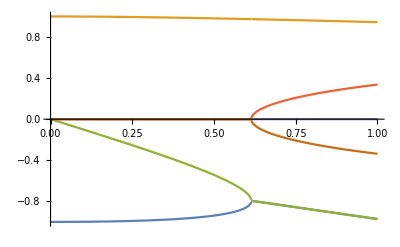

```mathematica
Plot[Evaluate[Flatten[{rootsr,rootsi}]],{i,0,1}]
```

```mathematica
sol=Flatten[N[Solve[(ch/.i-> .5)==0,z]]]
```

{z→-0.981425,z→0.542743,z→0.938682}

+++++++++++++++++++++++++++++++

Связь в терминах фазоров

```mathematica
mb:=({{ωx, q}, {q, ωy}});
```

```mathematica
Simplify[Det[mb-z({{1, 0}, {0, 1}})]]
```

-q^2+(z-ωx) (z-ωy)

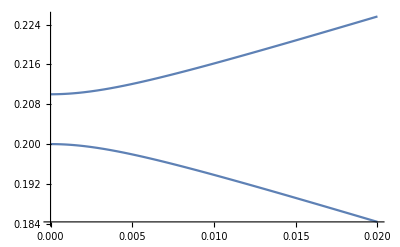

```mathematica
Plot[Eigenvalues[mb/.{ωx->.2,ωy->.21}],{q,0,.02}]
```

Связь, в терминах  x, px,  y, py.

Бетатронная матрица

```mathematica
mq=ArrayFlatten[{{({{1, 0}, {0, 1}}),({{0, 0}, {q, 0}})},{({{0, 0}, {q, 0}}),({{1, 0}, {0, 1}})}}]
```

{{1,0,0,0},{0,1,q,0},{0,0,1,0},{q,0,0,1}}

```mathematica
mb4=Simplify[mq.{{Cos[2 π νx],Sin[2 π νx],0,0},{-Sin[2 π νx],Cos[2 π νx],0,0},{0,0,Cos[2 π νy],Sin[2 π νy]},{0,0,-Sin[2 π νy],Cos[2 π νy]}}];
```

```mathematica
Simplify[Det[mb4-z IdentityMatrix[4]]]
```

1+2 z^2+z^4-2 (z+z^3) Cos[2 π νx]-1/2 (-4+q^2) z^2 Cos[2 π (νx-νy)]-2 z Cos[2 π νy]-2 z^3 Cos[2 π νy]+2 z^2 Cos[2 π (νx+νy)]+1/2 q^2 z^2 Cos[2 π (νx+νy)]

```mathematica
Chop[Log[Eigenvalues[mb4/.{νx->.2,νy->.208}]/.q->.0]/(2 π ⅈ)]
```

{-0.208,0.208,-0.2,0.2}

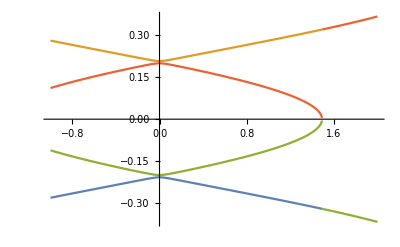

```mathematica
Plot[Evaluate[Chop[Log[Eigenvalues[mb4/.{νx->.2,νy->.208}]]/(2 π ⅈ)]],{q,-1,2},PlotRange->All]
```

Циркулянта

```mathematica
cir=Simplify[MatrixExp[2 π ⅈ νs mc3]]
```

{{1/3 (1+2 Cos[2 π νs]),2/3 Sin[π νs] (√3 Cos[π νs]+Sin[π νs]),-2/3 (√3 Cos[π νs]-Sin[π νs]) Sin[π νs]},{-2/3 (√3 Cos[π νs]-Sin[π νs]) Sin[π νs],1/3 (1+2 Cos[2 π νs]),2/3 Sin[π νs] (√3 Cos[π νs]+Sin[π νs])},{2/3 Sin[π νs] (√3 Cos[π νs]+Sin[π νs]),-2/3 (√3 Cos[π νs]-Sin[π νs]) Sin[π νs],1/3 (1+2 Cos[2 π νs])}}

Синхробетатронная матрица

```mathematica
mm=Direct[cir/.νs->0.01,mb4/.{νx->.2,νy->.208}];
```

```mathematica
Dimensions[mm]
```

{12,12}

```mathematica
Table[Chop[Log[Eigenvalues[mm]]/(2 π ⅈ)],{q,0,.2,.2}]
```

{{-0.208-0.01 ⅈ,0.208-0.01 ⅈ,0.2-0.01 ⅈ,-0.2-0.01 ⅈ,-0.208,0.2,0.208,-0.2,-0.208+0.01 ⅈ,0.208+0.01 ⅈ,-0.2+0.01 ⅈ,0.2+0.01 ⅈ},{-0.18732-0.01 ⅈ,-0.220203-0.01 ⅈ,0.220203-0.01 ⅈ,0.18732-0.01 ⅈ,-0.18732,-0.220203,0.18732,0.220203,-0.18732+0.01 ⅈ,-0.220203+0.01 ⅈ,0.18732+0.01 ⅈ,0.220203+0.01 ⅈ}}

```mathematica
Eigenvalues[cir]
```

{1,1/3 (3 Cos[2 π νs]-3 ⅈ Sin[2 π νs]),1/3 (3 Cos[2 π νs]+3 ⅈ Sin[2 π νs])}

```mathematica
Синхробета - спектр  от  q
```

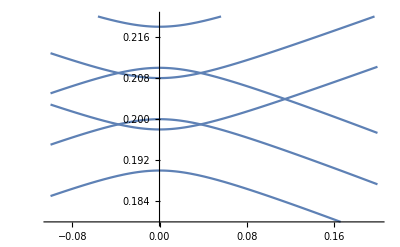

```mathematica
Plot[Sort[Chop[Log[Eigenvalues[mm]]/(2 π ⅈ)]],{q,-.1,.2},PlotRange->{.18,.22}]
```

Так  можно и дальше развивать

++++++++++++++++++++++++++++++++++++++++++ =

Однако, хочется через фазоры со связью

```mathematica
mb2:=({{2 π νx, q}, {q, 2 π νy}})
```

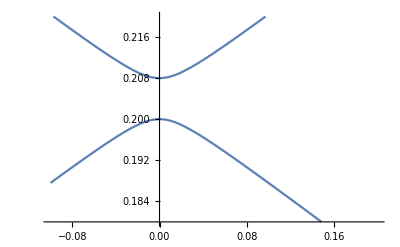

```mathematica
Plot[Sort[Chop[Eigenvalues[mb2/.{νx->.208,νy->.2}]/(2 π)]],{q,-.1,.2},PlotRange->{.18,.22}]
```

Синхробета  матрица  для связи

```mathematica
mmat=ArrayFlatten[{{mc3 0.01+IdentityMatrix[3] 0.207,q IdentityMatrix[3]},{q IdentityMatrix[3],mc3 0.01+IdentityMatrix[3] 0.2}}];
```

```mathematica
%//MatrixForm
```

(0.208 | 0.-0.0057735 ⅈ | 0.+0.0057735 ⅈ | q | 0 | 0
0.+0.0057735 ⅈ | 0.208 | 0.-0.0057735 ⅈ | 0 | q | 0
0.-0.0057735 ⅈ | 0.+0.0057735 ⅈ | 0.208 | 0 | 0 | q
q | 0 | 0 | 0.2 | 0.-0.0057735 ⅈ | 0.+0.0057735 ⅈ
0 | q | 0 | 0.+0.0057735 ⅈ | 0.2 | 0.-0.0057735 ⅈ
0 | 0 | q | 0.-0.0057735 ⅈ | 0.+0.0057735 ⅈ | 0.2)

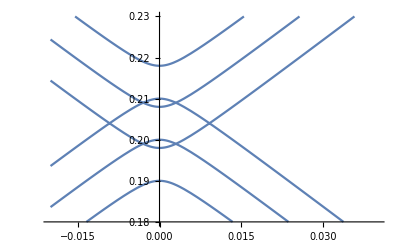

```mathematica
Plot[Sort[Chop[Eigenvalues[mmat]]],{q,-.02,.04},PlotRange->{.18,.23}]
```

```mathematica
Eigenvalues[mmat/.q->.015]
```

{0.229524,0.219524,0.209524,0.198476,0.188476,0.178476}

```mathematica
Eigenvalues[mmat/.q->.0001]
```

{0.218001,0.209999,0.208001,0.199999,0.198001,0.189999}

А теперь  wake  общего вида “тензорный”

```mathematica
mw:=-Direct[({{Wxx, Wxy}, {Wyx, Wyy}}),({{1, 0, 1}, {2, 1, 2}, {1, 0, 1}})]curr/3
```

```mathematica
mw//MatrixForm
```

((curr Wxx)/3 | 0 | (curr Wxx)/3 | (curr Wxy)/3 | 0 | (curr Wxy)/3
(2 curr Wxx)/3 | (curr Wxx)/3 | (2 curr Wxx)/3 | (2 curr Wxy)/3 | (curr Wxy)/3 | (2 curr Wxy)/3
(curr Wxx)/3 | 0 | (curr Wxx)/3 | (curr Wxy)/3 | 0 | (curr Wxy)/3
(curr Wyx)/3 | 0 | (curr Wyx)/3 | (curr Wyy)/3 | 0 | (curr Wyy)/3
(2 curr Wyx)/3 | (curr Wyx)/3 | (2 curr Wyx)/3 | (2 curr Wyy)/3 | (curr Wyy)/3 | (2 curr Wyy)/3
(curr Wyx)/3 | 0 | (curr Wyx)/3 | (curr Wyy)/3 | 0 | (curr Wyy)/3)

Простейший пример

```mathematica
Wxx=1; Wxy=0; Wyx=0; Wyy=0;
```

```mathematica
Eigenvalues[(mmat/.q->0)+(mw/.curr->0.)]
```

{0.218,0.21,0.208,0.2,0.198,0.19}

Wake  only  xx, no   x - y   coupling

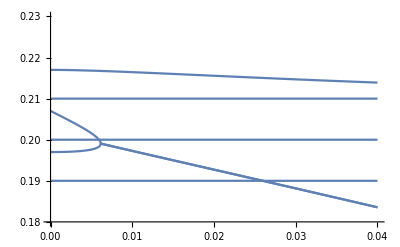

```mathematica
Plot[Sort[Re[Chop[Eigenvalues[(mmat/.q->0)+mw]]]],{curr,0,.04},PlotRange->{.18,.23}]
```

Добавили  связь

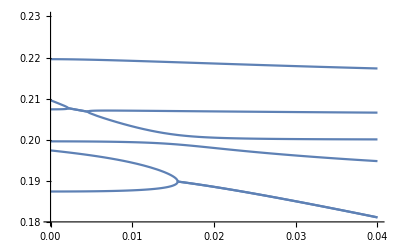

```mathematica
Plot[Sort[Re[Chop[Eigenvalues[(mmat/.q->0.005)+mw]]]],{curr,0,.04},PlotRange->{.18,.23}]
```

Ещё  увеличили

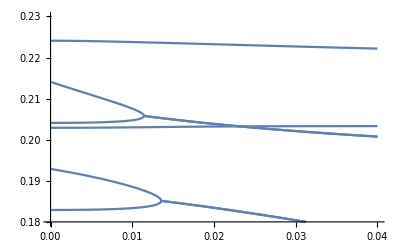

```mathematica
Plot[Sort[Re[Chop[Eigenvalues[(mmat/.q->0.01)+mw]]]],{curr,0,.04},PlotRange->{.18,.23}]
```

Теперь  wake  "yy"

```mathematica
Wxx=0; Wxy=0; Wyx=0; Wyy=1;
```

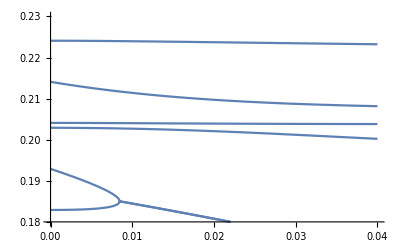

```mathematica
Plot[Sort[Re[Chop[Eigenvalues[(mmat/.q->0.01)+mw]]]],{curr,0,.04},PlotRange->{.18,.23}]
```

Перекрёстный  wake

```mathematica
Wxx=0; Wxy=0; Wyx=1; Wyy=0;
```

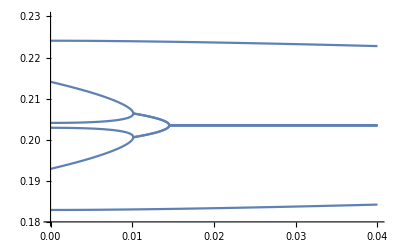

```mathematica
Plot[Sort[Re[Chop[Eigenvalues[(mmat/.q->0.01)+mw]]]],{curr,0,.04},PlotRange->{.18,.23}]
```

Другой перекрёстный  wake

```mathematica
Wxx=0; Wxy=1; Wyx=0; Wyy=0;
```

```mathematica
Plot[Sort[Re[Chop[Eigenvalues[(mmat/.q->0.01)+mw]]]],{curr,0,.04},PlotRange->{.18,.23}]
```

-Graphics-

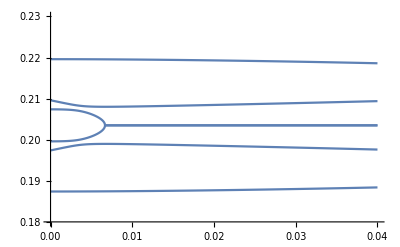

```mathematica
Plot[Sort[Re[Chop[Eigenvalues[(mmat/.q->0.005)+mw]]]],{curr,0,.04},PlotRange->{.18,.23}]
```

```mathematica
Wxx=0; Wxy=0; Wyx=1; Wyy=0;
```

```mathematica
Plot[Sort[Re[Chop[Eigenvalues[(mmat/.q->0.005)+mw]]]],{curr,0,.04},PlotRange->{.18,.23}]
```

-Graphics-